```mathematica
FvmBVP[n_,δ_,b_,f_,T_,g2_,ψ_,uuu_]:=Module[{h,x,xd,t=0,a,b0,aaa,bbb,kk,aaa0,tm,dltt,u0,u00,urep,u1,var,varinit,eq0,eqn,eqnn,sol,i},
h=(b-δ)/n;xd=Table[δ+i h,{i,0,n,1}];
u0=ψ[xd];u00=ψ[δ-h];dltt=2*h;
var=Table[u1[i],{i,1,n-1}];
var=PrependTo[var,b0];
aaa={0,1,-1,2,-6};(*增广初值*)
aaa0=aaa;
While[t<T,
t=t+dltt;tm=t-dltt/2;aaa0[[-1]]=b0;u1[n]=g2[t];
For[kk=2,kk≤Length[aaa0],kk++,
aaa0[[-kk]]=aaa[[-kk]]+dltt/2*(aaa[[-kk+1]]+aaa0[[-kk+1]]);];
urep[x_,b0_]=uuu[x,t]/.c0[t]->(aaa0[[-5]])/.c0'[t]->(aaa0[[-4]])/.c0''[t]->(aaa0[[-3]])/.Derivative[3][c0][t]->(aaa0[[-2]])/.Derivative[4][c0][t]->(aaa0[[-1]])//Simplify;(*多变单*)
u1[-1]=urep[δ-h,b0]//Simplify;
u1[0]=urep[xd[[1]],b0]//Simplify;

varinit=Transpose[{var,Drop[u0,-1]}];
eq0=(u1[0]-u0[[1]])*h/dltt+2/h*(u1[0]^3+u0[[1]]^3+u1[-1]^3+u00^3)/2*(u1[0]+u0[[1]]-u1[-1]-u00)/2-2/h*(u1[0]^3+u0[[1]]^3+u1[1]^3+u0[[2]]^3)/2*(u1[1]+u0[[2]]-u1[0]-u0[[1]])/2-h f[xd[[1]],tm,(u1[0]+u0[[1]])/2]==0;
eqn=Table[(u1[i]-u0[[i+1]])*h/dltt+2/h*(u1[i]^3+u0[[i+1]]^3+u1[i-1]^3+u0[[i]]^3)/2*(u1[i]+u0[[i+1]]-u1[i-1]-u0[[i]])/2-2/h*(u1[i]^3+u0[[i+1]]^3+u1[i+1]^3+u0[[i+2]]^3)/2*(u1[i+1]+u0[[i+2]]-u1[i]-u0[[i+1]])/2-h f[xd[[i+1]],tm,(u1[i]+u0[[i+1]])/2]==0,{i,n-1}];
eqn=PrependTo[eqn,eq0];
sol=FindRoot[eqn,varinit];
u0=var/.sol;
a=u0[[1]];
u00=urep[δ-h,b0]/.b0->a;
u0[[1]]=urep[δ,b0]/.b0->a;
AppendTo[u0,u1[n]];
bbb=aaa;
aaa[[-1]]=a;
For[kk=2,kk≤Length[aaa],kk++,
aaa[[-kk]]=bbb[[-kk]]+dltt/2*(aaa[[-kk+1]]+bbb[[-kk+1]]);
];
];{t,xd,u0,a}];
```

```mathematica
Clear["*"];
```

```mathematica
uexact[x_,t_]:=(Sin[x]Log[1+x+t])^(1/4)
```

```mathematica
δ=0.2;b=1;
g2[t_]=uexact[b,t];
ψ[x_]=uexact[x,0]
```

(Log[1+x] Sin[x])^(1/4)

```mathematica
f[x_,t_,u_]:=-(2 Cos[x])/(1+t+x)+(Sin[x]/(1+t+x)^2+u^4+Sin[x]/(4 (1+t+x) u^3))
```

```mathematica
T=0.4
```

0.4

```mathematica
n=128
```

128

```mathematica
uuu[x_,t_]:=(x^2/(1+t)+x c0[t]+(x^(9/4) (-4+4 (1+t) c0'[t]))/(45 (1+t) c0[t]^(3/4))+(x^3 (-1-t-12 (x c0[t])^(3/4)-4 (1+t)^2 c0[t] (x c0[t])^(3/4)+(1+t)^2 c0'[t]))/(24 (1+t)^2 (x c0[t])^(3/4))+1/(46080 (1+t)^5 c0[t]^3 (x c0[t])^(3/4))x^6 (128 (55-28 t-2 t^2+12 t^3+3 t^4) c0[t]^3 (x c0[t])^(3/4)-231 (1+t) (-1+(1+t) c0'[t])-252 (1+t) c0[t] (-1+(1+t) c0'[t])+12 (-7-5 t+3 t^2+t^3) c0[t]^2 (-1+(1+t) c0'[t]))-(x^4 (32 (-1+2 t+t^2)+(3 (1+t) x (-1+(1+t) c0'[t]))/(x c0[t])^(7/4)))/(192 (1+t)^3)+1/(7680 (1+t)^4 c0[t]^2 (x c0[t])^(3/4))x^5 (64 (1+t)^4 c0[t]^3 (x c0[t])^(3/4)+63 (1+t) (-1+(1+t) c0'[t])+36 (1+t) c0[t] (-1+(1+t) c0'[t])+4 c0[t]^2 (1+t^3-320 (x c0[t])^(3/4)+t^2 (3+160 (x c0[t])^(3/4))+t (3+320 (x c0[t])^(3/4))-(1+t)^4 c0'[t]))+1/(5160960 (1+t)^6 c0[t]^4 (x c0[t])^(3/4))x^7 (-1024 (1+t)^6 c0[t]^5 (x c0[t])^(3/4)+17325 (1+t) (-1+(1+t) c0'[t])+27720 (1+t) c0[t] (-1+(1+t) c0'[t])-840 (-21-19 t+3 t^2+t^3) c0[t]^2 (-1+(1+t) c0'[t])-480 (-11-9 t+3 t^2+t^3) c0[t]^3 (-1+(1+t) c0'[t])-16 c0[t]^4 (-1-t^5+41664 (x c0[t])^(3/4)+t^4 (-5+1344 (x c0[t])^(3/4))+2 t^3 (-5+2688 (x c0[t])^(3/4))-2 t^2 (5+2688 (x c0[t])^(3/4))-t (5+21504 (x c0[t])^(3/4))+(1+t)^6 c0'[t]))+1/(342720 (1+t)^3 c0[t]^(11/4) (x c0[t])^(3/4))x^(21/4) (703-1793 (1+t) c0'[t]+1090 (1+t)^2 c0'[t]^2+4 c0[t] (-4 (31+15 (x c0[t])^(3/4)+15 t (x c0[t])^(3/4))+15 (1+t+4 (x c0[t])^(3/4)+8 t (x c0[t])^(3/4)+4 t^2 (x c0[t])^(3/4)) c0'[t]-109 (1+t)^2 c0''[t]))-(47 x^(17/4) (3-9 (1+t) c0'[t]+6 (1+t)^2 c0'[t]^2+4 c0[t] (-1-4 (x c0[t])^(3/4)-4 t (x c0[t])^(3/4)+4 (1+t)^2 (x c0[t])^(3/4) c0'[t]-(1+t)^2 c0''[t])))/(79560 (1+t)^2 c0[t]^(7/4) (x c0[t])^(3/4))+1/(2673216000 (1+t)^4 c0[t]^(15/4) (x c0[t])^(3/4))x^(25/4) (-4641 (1151-2773 (1+t) c0'[t]+1622 (1+t)^2 c0'[t]^2)-12 c0[t]^2 (-98885+16158 t+8079 t^2-31824 (x c0[t])^(3/4)-31824 t (x c0[t])^(3/4)-9 (1+t) (925+2693 t^2-3536 (x c0[t])^(3/4)+t (5386-3536 (x c0[t])^(3/4))) c0'[t]+16158 (1+t)^4 c0'[t]^2-91052 (1+t)^2 c0''[t])-2652 c0[t] (-18 (19+14 (x c0[t])^(3/4)+14 t (x c0[t])^(3/4))+(-1499+252 (x c0[t])^(3/4)+252 t^2 (x c0[t])^(3/4)+t (-1499+504 (x c0[t])^(3/4))) c0'[t]+1030 (1+t)^2 c0'[t]^2-811 (1+t)^2 c0''[t])+16 (1+t)^2 c0[t]^3 (8079-50780 (x c0[t])^(3/4)-50780 t (x c0[t])^(3/4)+50780 (1+t)^2 (x c0[t])^(3/4) c0'[t]+8079 (1+t)^2 c0''[t]))+1/(611631820800 (1+t)^4 c0[t]^(9/2) (x c0[t])^(3/4))x^(13/2) (159547643-625257357 (1+t) c0'[t]+802988745 (1+t)^2 c0'[t]^2-337279031 (1+t)^3 c0'[t]^3-2 c0[t] (13 (6573649+1349760 (x c0[t])^(3/4)+1349760 t (x c0[t])^(3/4))+195 (1+t)^2 (57899+139520 (x c0[t])^(3/4)+139520 t (x c0[t])^(3/4)) c0'[t]^2+82775452 (1+t)^2 c0''[t]-2 (1+t) c0'[t] (57245951+22376640 (x c0[t])^(3/4)+22376640 t (x c0[t])^(3/4)+50259806 (1+t)^2 c0''[t]))+3840 c0[t]^2 (8784+6448 (x c0[t])^(3/4)+6448 t (x c0[t])^(3/4)-390 (1+t+2 (x c0[t])^(3/4)+4 t (x c0[t])^(3/4)+2 t^2 (x c0[t])^(3/4)) c0'[t]+52 (1+t)^2 (31+109 (x c0[t])^(3/4)+109 t (x c0[t])^(3/4)) c0''[t]-3391 Derivative[3][c0][t]-10173 t Derivative[3][c0][t]-10173 t^2 Derivative[3][c0][t]-3391 t^3 Derivative[3][c0][t]))-1/(30245529600 (1+t)^3 c0[t]^(7/2) (x c0[t])^(3/4))47 x^(11/2) (81349-343809 (1+t) c0'[t]+472371 (1+t)^2 c0'[t]^2-209911 (1+t)^3 c0'[t]^3-8 c0[t] (14707+5760 (x c0[t])^(3/4)+5760 t (x c0[t])^(3/4)+11520 (1+t)^3 (x c0[t])^(3/4) c0'[t]^2+16147 c0''[t]+32294 t c0''[t]+16147 t^2 c0''[t]-(1+t) c0'[t] (19027+17280 (x c0[t])^(3/4)+17280 t (x c0[t])^(3/4)+20467 (1+t)^2 c0''[t]))+15360 c0[t]^2 (2+4 (x c0[t])^(3/4)+4 t (x c0[t])^(3/4)+4 (1+t)^3 (x c0[t])^(3/4) c0''[t]-(1+t)^3 Derivative[3][c0][t]))-(47 x^(27/4) (536586203-2954538869 (1+t) c0'[t]+6032190189 (1+t)^2 c0'[t]^2-5405860583 (1+t)^3 c0'[t]^3+1791623060 (1+t)^4 c0'[t]^4+12 c0[t] (-74705473-13015840 (x c0[t])^(3/4)-13015840 t (x c0[t])^(3/4)+33585760 (1+t)^4 (x c0[t])^(3/4) c0'[t]^3-83508433 c0''[t]-167016866 t c0''[t]-83508433 t^2 c0''[t]-3 (1+t)^2 c0'[t]^2 (42332571+25193120 (x c0[t])^(3/4)+25193120 t (x c0[t])^(3/4)+46534091 (1+t)^2 c0''[t])+2 (1+t) c0'[t] (98029193+27504720 (x c0[t])^(3/4)+27504720 t (x c0[t])^(3/4)+108732953 (1+t)^2 c0''[t]))-3840 c0[t]^2 (-102837-58828 (x c0[t])^(3/4)-58828 t (x c0[t])^(3/4)-2 (1+t)^2 (36199+32294 (x c0[t])^(3/4)+32294 t (x c0[t])^(3/4)) c0''[t]-39079 (1+t)^4 c0''[t]^2+36199 Derivative[3][c0][t]+108597 t Derivative[3][c0][t]+108597 t^2 Derivative[3][c0][t]+36199 t^3 Derivative[3][c0][t]+(1+t) c0'[t] (86798+76108 (x c0[t])^(3/4)+76108 t (x c0[t])^(3/4)+81868 (1+t)^3 (x c0[t])^(3/4) c0''[t]-44839 (1+t)^3 Derivative[3][c0][t]))+7372800 c0[t]^3 (-2 (3+4 (x c0[t])^(3/4)+4 t (x c0[t])^(3/4))+4 (1+t)^4 (x c0[t])^(3/4) Derivative[3][c0][t]-(1+t)^4 Derivative[4][c0][t])))/(2253896865792000 (1+t)^4 c0[t]^(21/4) (x c0[t])^(3/4)))^(1/4)
```

```mathematica
res=FvmBVP[n,δ,b,f,T,g2,ψ,uuu]
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{0.4,{0.2,0.20625,0.2125,0.21875,0.225,0.23125,0.2375,0.24375,0.25,0.25625,0.2625,0.26875,0.275,0.28125,0.2875,0.29375,0.3,0.30625,0.3125,0.31875,0.325,0.33125,0.3375,0.34375,0.35,0.35625,0.3625,0.36875,0.375,0.38125,0.3875,0.39375,0.4,0.40625,0.4125,0.41875,0.425,0.43125,0.4375,0.44375,0.45,0.45625,0.4625,0.46875,0.475,0.48125,0.4875,0.49375,0.5,0.50625,0.5125,0.51875,0.525,0.53125,0.5375,0.54375,0.55,0.55625,0.5625,0.56875,0.575,0.58125,0.5875,0.59375,0.6,0.60625,0.6125,0.61875,0.625,0.63125,0.6375,0.64375,0.65,0.65625,0.6625,0.66875,0.675,0.68125,0.6875,0.69375,0.7,0.70625,0.7125,0.71875,0.725,0.73125,0.7375,0.74375,0.75,0.75625,0.7625,0.76875,0.775,0.78125,0.7875,0.79375,0.8,0.80625,0.8125,0.81875,0.825,0.83125,0.8375,0.84375,0.85,0.85625,0.8625,0.86875,0.875,0.88125,0.8875,0.89375,0.9,0.90625,0.9125,0.91875,0.925,0.93125,0.9375,0.94375,0.95,0.95625,0.9625,0.96875,0.975,0.98125,0.9875,0.99375,1.},{0.552783,0.558144,0.563412,0.568591,0.573686,0.578698,0.583633,0.588492,0.59328,0.597998,0.602649,0.607236,0.611761,0.616225,0.620632,0.624982,0.629277,0.63352,0.63771,0.641851,0.645944,0.649989,0.653988,0.657942,0.661853,0.665721,0.669547,0.673333,0.677079,0.680786,0.684455,0.688087,0.691683,0.695243,0.698768,0.702259,0.705717,0.709141,0.712533,0.715894,0.719223,0.722522,0.72579,0.729029,0.732239,0.735421,0.738574,0.741699,0.744797,0.747868,0.750913,0.753931,0.756924,0.759892,0.762834,0.765752,0.768645,0.771514,0.774359,0.777181,0.77998,0.782756,0.78551,0.788241,0.79095,0.793637,0.796302,0.798946,0.801569,0.804172,0.806753,0.809314,0.811855,0.814376,0.816876,0.819358,0.821819,0.824262,0.826685,0.82909,0.831475,0.833842,0.836191,0.838521,0.840833,0.843128,0.845404,0.847663,0.849904,0.852128,0.854334,0.856523,0.858696,0.860851,0.86299,0.865112,0.867217,0.869306,0.871379,0.873435,0.875476,0.8775,0.879509,0.881502,0.883479,0.88544,0.887386,0.889317,0.891232,0.893132,0.895017,0.896887,0.898742,0.900582,0.902407,0.904218,0.906013,0.907795,0.909561,0.911314,0.913052,0.914775,0.916485,0.91818,0.919861,0.921528,0.923181,0.92482,0.926446},6922.42}

```mathematica
err=uexact[res[[2]],res[[1]]]-res[[3]]
```

{4.40843×10^-6,4.3575×10^-6,4.30464×10^-6,4.23883×10^-6,4.16506×10^-6,4.0902×10^-6,4.019×10^-6,3.9537×10^-6,3.89473×10^-6,3.84148×10^-6,3.79293×10^-6,3.74799×10^-6,3.70569×10^-6,3.66523×10^-6,3.62601×10^-6,3.5876×10^-6,3.54969×10^-6,3.51207×10^-6,3.47459×10^-6,3.43716×10^-6,3.3997×10^-6,3.36217×10^-6,3.32453×10^-6,3.28676×10^-6,3.24883×10^-6,3.21074×10^-6,3.17246×10^-6,3.134×10^-6,3.09536×10^-6,3.05653×10^-6,3.01754×10^-6,2.97839×10^-6,2.93909×10^-6,2.89967×10^-6,2.86014×10^-6,2.82053×10^-6,2.78085×10^-6,2.74114×10^-6,2.7014×10^-6,2.66168×10^-6,2.62198×10^-6,2.58234×10^-6,2.54277×10^-6,2.5033×10^-6,2.46394×10^-6,2.42471×10^-6,2.38564×10^-6,2.34674×10^-6,2.30802×10^-6,2.26949×10^-6,2.23118×10^-6,2.19308×10^-6,2.15522×10^-6,2.1176×10^-6,2.08022×10^-6,2.04311×10^-6,2.00625×10^-6,1.96967×10^-6,1.93335×10^-6,1.89732×10^-6,1.86156×10^-6,1.82608×10^-6,1.79089×10^-6,1.75599×10^-6,1.72137×10^-6,1.68704×10^-6,1.65299×10^-6,1.61923×10^-6,1.58576×10^-6,1.55256×10^-6,1.51966×10^-6,1.48703×10^-6,1.45468×10^-6,1.42261×10^-6,1.39081×10^-6,1.35929×10^-6,1.32803×10^-6,1.29705×10^-6,1.26632×10^-6,1.23586×10^-6,1.20565×10^-6,1.1757×10^-6,1.14599×10^-6,1.11654×10^-6,1.08733×10^-6,1.05836×10^-6,1.02964×10^-6,1.00114×10^-6,9.72879×10^-7,9.44845×10^-7,9.17036×10^-7,8.89449×10^-7,8.62081×10^-7,8.34929×10^-7,8.0799×10^-7,7.81261×10^-7,7.54739×10^-7,7.28421×10^-7,7.02305×10^-7,6.76388×10^-7,6.50668×10^-7,6.25142×10^-7,5.99807×10^-7,5.74662×10^-7,5.49704×10^-7,5.24931×10^-7,5.0034×10^-7,4.75928×10^-7,4.51694×10^-7,4.27634×10^-7,4.03746×10^-7,3.80026×10^-7,3.5647×10^-7,3.33074×10^-7,3.09835×10^-7,2.86747×10^-7,2.63806×10^-7,2.41007×10^-7,2.18345×10^-7,1.95816×10^-7,1.73417×10^-7,1.51147×10^-7,1.29009×10^-7,1.07009×10^-7,8.51626×10^-8,6.34923×10^-8,4.2035×10^-8,2.0845×10^-8,1.11022×10^-16}

```mathematica
emax8=Max[Abs[err]]
```

0.00133319

```mathematica
emax16=Max[Abs[err]]
```

0.000308071

```mathematica
emax32=Max[Abs[err]]
```

0.0000745294

```mathematica
emax64=Max[Abs[err]]
```

0.0000178565

```mathematica
emax128=Max[Abs[err]]
```

4.40843×10^-6

```mathematica
emax=Log2[{emax8/emax16,emax16/emax32,emax32/emax64,emax64/emax128}]
```

{2.11355,2.04738,2.06136,2.01811}

```mathematica
em8=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]]
```

0.000772477

```mathematica
em16=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]]
```

0.000165777

```mathematica
em32=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]]
```

0.0000371958

```mathematica
em64=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]]
```

8.75336×10^-6

```mathematica
em128=Sqrt[Sum[(err[[i]])^2*(b-δ)/n,{i,1,n}]]
```

2.02955×10^-6

```mathematica
em=Log2[{em8/em16,em16/em32,em32/em64,em64/em128}]
```

{2.22025,2.15603,2.08723,2.10868}

```mathematica
emh18=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*8*)
```

0.00152735

```mathematica
emh116=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*16*)
```

0.000369096

```mathematica
emh132=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*32*)
```

0.000088577

```mathematica
emh164=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*64*)
```

0.0000209264

```mathematica
emh1128=Sqrt[Sum[(err[[i]]-err[[i-1]])^2/((b-δ)/n),{i,2,n}]](*128*)
```

5.14143×10^-6

```mathematica
emh=Log2[{emh18/emh116,emh116/emh132,emh132/emh164,emh164/emh1128}]
```

{2.04896,2.05899,2.08161,2.02508}

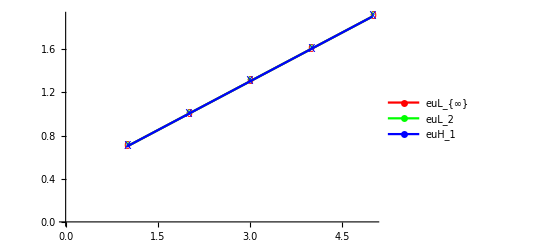

```mathematica
x=Table[-Log[10,0.2/(2^(i-1))],{i,1,5}];
y1=Table[-Log[10,emax[4*(i-1)+1]],{i,1,5}];
y2=Table[-Log[10,em[4*(i-1)+2]],{i,1,5}];
y3=Table[-Log[10,emh[4*(i-1)+3]],{i,1,5}];

(*绘图*)
aaa=ListLinePlot[{x,y1},PlotStyle->Red,PlotLegends->{"euL_{∞}"},PlotMarkers->"0"];
bbb=ListLinePlot[{x,y2},PlotStyle->Green,PlotLegends->{"euL_2"},PlotMarkers->"*"];
ccc=ListLinePlot[{x,y3},PlotStyle->Blue,PlotLegends->{"euH_1"},PlotMarkers->"X"];
Show[aaa,bbb,ccc]
```